```mathematica
Clear["Global`*"]
```

Para inicio, devemos estabelecer as equações de movimento para as partes dos sistema sendo elas a maquina disparadora de pratos e a besta

```mathematica
EqMaqy[t_] = vm t - g t ^2/2;
EqMaqx[t_]  = x0;
EqBestay[t_] = vb Sin[θ] t - g t ^2/2;
EqBestax[t_] = vb Cos[θ] t ;
```

Tendo as equações definidas, podemos relaciona-las através do tempo. O tempo será fundamental em cada passo que virá a seguir. Podemos agora encontrar o tempo de disparo da besta. Ele é dado pelo momento em que o prato começa a descer. Em termos matemáticos, esse tempo será quando a velocidade do prato se iguale à zero. Ou seja, o momento em que sua derivada seja zero

```mathematica
tDisparo = t /. Solve[EqMaqy'[t] == 0, t];
```

Com esse valor de tempo, podemos descobrir a altura maxima de alcance do prato, que será fundamental para encontrar o valor do ângulo do disparo. Substituindo o tDisparo na equação de posição, teremos a altura máxima. Com isso em mãos, podemos utilizar do conceito de trigonometria. Como a maquina faz um disparo unicamente vertical, gera um ângulo de 90° com o horizonte, tendo, então, um triângulo retângulo. Desta forma, a tangente do ângulo θ será o cateto oposto dividido pelo adjacente. De forma análoga, nosso ângulo teta será dado pela arctangete da altura maxima do prato dividido pela distancia entre o atirador e máquina, da seguinte forma.

```mathematica
-Graphics-;
```

Em termos matemáticos, podemos defini-la como

```mathematica
θ = ArcTan[EqMaqy[tDisparo]/x0];
```

Uma vez com o ângulo determinado, pode-se agora determinar a velocidade de disparo do projétil. Utilizando da componente vertical, não se tem muito a fazer porque tendo ele sido disparado, não há muitas relações com a componente vertical do prato. Apenas que ambos estão sobre a interação da gravidade e assim, caindo em queda livre. Já no eixo horizontal, para que a flecha atinja o prato, não existe sentido pensar que ela viajou uma distância inferior à x0. Desta forma, podemos estabelecer uma relação entre vb e x0

```mathematica
vb = vb/.Solve[EqBestax[t-tDisparo]==x0,vb];
```

Observação: O tempo usado será t - tDisparo pois a besta só dispara após o prato começar a cair. Assim, t - tDisparo é o tempo de viagem do projétil.
Assim sendo, todas as equações estão relacionadas e podem ser obtidas em função da velocidade de disparo da maquina, tempo, gravidade e distancia entre maquina e atirador

```mathematica
EqBestax[t] // PowerExpand
EqBestay[t] //PowerExpand
```

{(t √(vm^4+4 g^2 x0^2))/(2 (g t-vm) √(1+vm^4/(4 g^2 x0^2)))}

{-(g t^2)/2+(t vm^2 √(vm^4+4 g^2 x0^2))/(4 g (g t-vm) √(1+vm^4/(4 g^2 x0^2)) x0)}

Agora, definindo os valores de distancia e gravidade podemos plotar um grafico parametrico para diferentes velocidades de lançamento do prato. Para facilitar as demonstranções, vamos assumir um valor fixo de velocidade e ângulos varáveis.

```mathematica
valores = {g -> 9.8, x0 -> 60};
vb = 100;
posProjetil[t_] :={ EqBestax[t], EqBestay[t]}
```

```mathematica
plot[flecha_] := ParametricPlot[posProjetil[t] //. valores/.{vm-> flecha} ,{t,0,10} ]
```

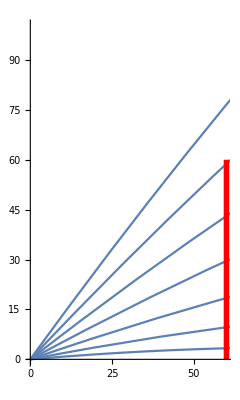

```mathematica
Show[Table[plot[fl],{fl,10,40,5}],PlotRange-> {{0,60},{0,100}},Epilog-> {Thickness[0.01],Hue[1.],Line[{{60,60},{60,0}}]}]
```

Agora, para construir a animação, usaremos apenas dois valores de velocidade de lançamento da máquina. A primeira animação mostra a flecha acertando o prato. Enquanto a segunda, devido a alteração na velocidade, mostra o tiro errado.

```mathematica
val = {g-> 9.8, x0->60, vm -> 20};
vb = 40;
tDisparo = tDisparo  /. val;
```

```mathematica
eqx[t_] = EqBestax[t] /. val;
eqy[t_] = EqBestay[t] /. val;
eqmx[t_] = EqMaqx[t] /. val;
eqmy[t_] = EqMaqy[t] /. val;
```

```mathematica
param = ParametricPlot[{eqx[t][[1]],eqy[t][[1]]},{t,0,10} , AxesLabel->{"x","y"}, PlotRange->{{0,100},{0,30}}];
```

```mathematica
Animate[Show[param, Graphics[{
Red,PointSize[.02],
Point[{eqx[T - tDisparo[[1]]][[1]],eqy[T - tDisparo[[1]]][[1]]}],
 Point[{eqmx[T],eqmy[T]}] 
}]],{T,0,10,1/60}]
```

```mathematica
Animate[Show[param, Graphics[{
Red,PointSize[.02],
Point[{eqx[T+ 2 - tDisparo[[1]]][[1]],eqy[T+1.5- tDisparo[[1]]][[1]]}],
 Point[{eqmx[T],eqmy[T]}] 
}]],{T,0,10,1/60}]
```